```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/silvestre_parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
On[Assert]
```

```mathematica
ClearAll[J,P,Isospin,γMax,Λ,m1,m2,m3,projector,project,size,firstNonZero,ham,sM,t1,t2]
(**** !!!TUNABLE PARAMETERS!!! ****)
J=3/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=0;(* Isospin *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
m1=uq;(* mass of quark 1 *)
m2=uq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
excited=0;(* Choose excited state, 0 for ground state *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
project=If[m1==m2,True,False];
(* Obtain projector matrix *)
projector=Projector[J,P,Λ,γMax,Isospin];
(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,γMax,m1,m2,m3,1]];
Print["Time taken to compute t1: ",t1time]
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,γMax,m1,m2,m3,2]];
Print["Time taken to compute t2: ",t2time]
(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];
(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
firstNonZero=If[project==True,size-Total[Diagonal[projector]]+excited+1,1+excited];
ham[ω_]:=Hb[J,P,Isospin,Λ,γMax,ω,m1,m2,m3,project];
sM=stateMatrix[J,P,Λ,γMax];
```

Time taken to compute t1: 0.035241

Time taken to compute t2: 0.028857

Time taken to find minimum: 3.05317s

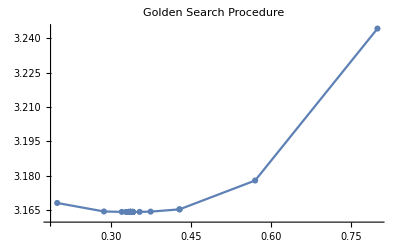

{ω_min,E_min}: {0.337420.00022,3.16434}

```mathematica
(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,firstNonZero,0.2,0.8,0.0005]];
wMin=(a+b)/2;
Print["Time taken to find minimum: ",minTime,"s"]
ListPlot[Sort[data],PlotRange->All,Joined->True,PlotMarkers->Automatic,PlotLabel->"Golden Search Procedure"]
eigvalMin=Eigenvalues[ham[wMin]][[-firstNonZero]];
Print["{ω_min,E_min}: ",{Around[wMin,a-wMin],eigvalMin}]
```

```mathematica
Eigenvalues[ham[0.337]]//Chop
```

{5.0326,4.99426,4.9515,4.93874,4.89069,4.81067,4.38687,4.3234,4.24001,4.12586,3.7917,3.6264,3.16434,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}